First assignment in coursera Machine Learning

```mathematica
A =IdentityMatrix[5];
MatrixForm[A]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
data = Import["/Users/casual/MEGA/Machine Learning Stuff/Coursera/Exercise 1/machine-learning-ex1/ex1/ex1data1.txt","Table"];

MatrixForm[data];
Dimensions[data];
Length[data]; (*gives rows*)

X = data[[All,1]];
MatrixForm[X]

Y = data[[All,2]];
MatrixForm[Y];
```

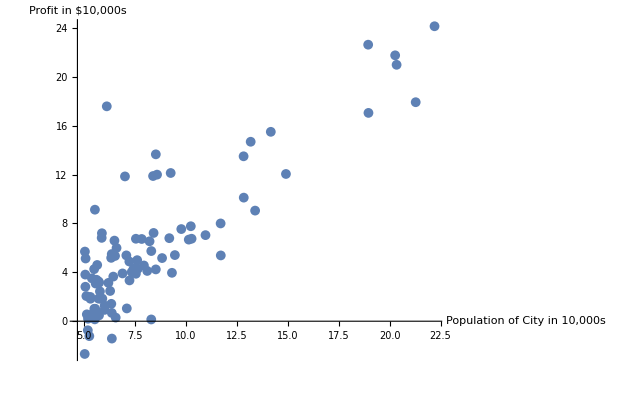

```mathematica
Show[%429,AxesLabel->{RawBoxes[RowBox[{RowBox[{"Population"," ","of"," ","City"," ","in"," ","10"}],",",RowBox[{"000","s"}]}]],RawBoxes[RowBox[{RowBox[{"Profit"," ","in"," ","$10"}],",",RowBox[{"000","s"}]}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Xintercept =Join[ConstantArray[1,{97,1}],data,2];
MatrixForm[Xintercept];

thetaVector = ConstantArray[0, {2,1}];
iterations = 1500;
alpha = 0.01;
```

```mathematica
thetaCost[ thetaRow0_, data0_]:=Module[{thetaRow = thetaRow0, data=data0},
yvalues[i0_]:=data[[i0,3]];
xvalues[i1_]:=data[[i1,2]];
theta = thetaVector[[thetaRow,1]];
thetaXvalues=data[[thetaRow,2]];
length = Length[data];
cost = 1/(2×length)×Sum[(xvalues[i]-yvalues[i])*thetaXvalues,{i,1,length}];
theta - alpha*cost
]
```

```mathematica
thetaCost[1, Xintercept]
```

Part::partd: Part specification x⟦1,2⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Indeterminate
```

```mathematica
thetaVector[[1,1]]
```

0